```mathematica
x
```

x

```mathematica
ImportDataset["10_40.mx"]
```

```mathematica
x
```

{k[k[k[k[k[k[s[s[k][s[s[k[k[s[k][s[1]]]][k[k[s[s[k[s]][k]]]]][k[k[k[s]]]]]]]]]][k[k[k[s[s][s[k]][s]]]][s]]]]]]→True,4998,k[s[s[1[1]]]][k]→False}
 |  |  |  |

```mathematica
lengths = x;
```

```mathematica
NoHalt = Select[lengths,#[[2]]==False&];
Halt = Select[lengths,#[[2]]==True&];
Length[NoHalt]
Length[Halt]
```

862

4138

```mathematica
HaltTrain = RandomSample[Halt,Length[NoHalt]];
```

```mathematica
HaltTrain[[1]]
```

s[k[s[k[s[k[k[s]]]]][k[s[k[s]][s[s]]]][s[k][s[k]][k]][k[s[s]][k]]]]→True

```mathematica
HaltTrainRaster=Monitor[Table[SKRasterize[HaltTrain[[x,1]],5]-> HaltTrain[[x,2]],{x,1,Length[HaltTrain]}],x];
```

```mathematica
NoHaltTrainRaster=Monitor[Table[SKRasterize[NoHalt[[x,1]],5]-> NoHalt[[x,2]],{x,1,Length[NoHalt]}],x];
```

```mathematica
RasterTrain = Join[HaltTrainRaster,NoHaltTrainRaster];
```

```mathematica
RasterClassify = Classify[RasterTrain]
```

ClassifierFunction[…]

0.818 accuracy (RandomForest) ... but is it just classifying based on the lines given?
0.758 accuracy with 5 lines.

#### Table of Results

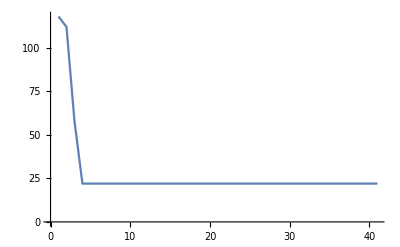
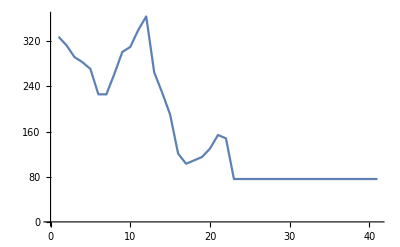
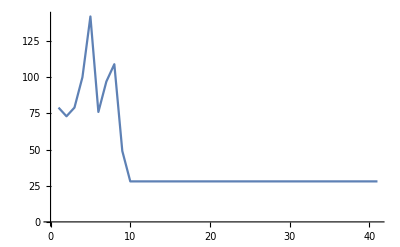
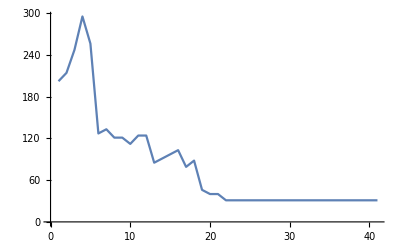
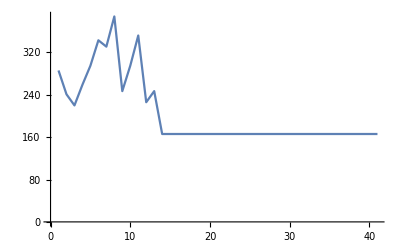
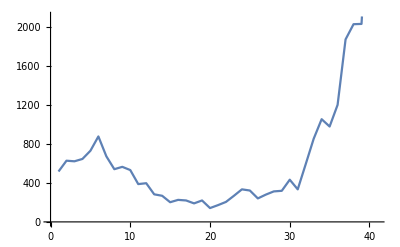
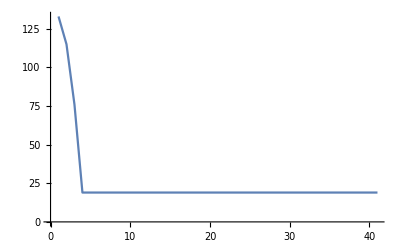
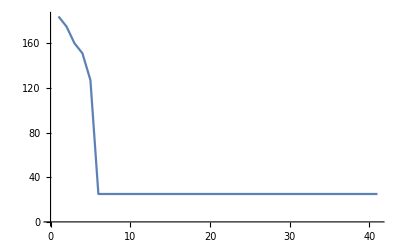
{{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False}}

```mathematica
Table[TestClassifierRasterize[RasterClassify,RasterTrain],50]
```

#### Thoughts

Perhaps it’s training on the last few lines of the raster. Try feature set identification:

```mathematica
rasternet = NetModel["VGG-16 Trained on ImageNet Competition Data"]
```

NetChain[<>]

```mathematica
rasterfeatureFunction=Take[rasternet,{1,"fc7"}]
```

NetChain[<>]

```mathematica
rastertraining = Keys[RasterTrain];
```

```mathematica
rasterfeatures=Monitor[Table[rasterfeatureFunction[rastertraining[[x]]],{x,1,Length[rastertraining]}],x];
```

```mathematica
xyz = DimensionReduce[features,3,Method->"TSNE"];
Graphics3D[
MapThread[Inset[Thumbnail[RemoveBackground@#2,32],#1]&,{xyz,rastertraining}],
BoxRatios->{1, 1, 1}
]
```

DimensionReduce::mlmpty: The dataset should contain at least one example.

MapThread::mptd: Object DimensionReduce[features,3,Method→TSNE] at position {2, 1} in MapThread[Inset[Thumbnail[RemoveBackground[#2],32],#1]&,{DimensionReduce[features,3,Method→TSNE],rastertraining}] has only 0 of required 1 dimensions.

-Graphics3D-